# Hypercube

### Author

Eric W. Weisstein
May 25, 2014

This notebook downloaded from http://mathworld.wolfram.com/notebooks/MultidimensionalGeometry/Hypercube.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Hypercube.html.

©2014 Wolfram Research, Inc. except for portions noted otherwise

### Code

```mathematica
edgefind::"usage"="edgefind[poly] returns the edges of equilateral regular polytopes."
mag::"usage"="mag[v_] returns the norm or magnitude of the n-vector 'v'."
nCube::"usage"="nCube[n] gives the 2^n vertices of an n-dimensional cube centered upon the origin, of edge length 2, and with its bounding hyperplanes parallel to the coordinate hyperplanes."
xyCube::"usage"="xyCube[n] gives the 2^n vertices of an n-dimensional cube centered upon the origin, of edge length Sqrt[2n], such that the projection into the {x,y} plane is isometric."
nCross::"usage"="nCross[n] gives the 2n vertices of an n-dimensional cross polytope or orthoplex, centered upon the origin, of edge length Sqrt[2], and unit circumradius."
xyCross::"usage"="xyCross[n] gives the 2^n vertices of an n-dimensional cross polytope centered upon the origin, of edge length Sqrt[n], such that the projection into the {x,y} plane is especially symmetrical."
nSimplex::"usage"="nSimplex[n] gives the (n+1) vertices of an n-simplex of edge Sqrt[n+1]."
zonotope::"usage"="zonotope[vectors] accepts a list of n-vectors 'vectors'. It returns 2^(Length[vectors]) n-vectors, which are the projection (possibly oblique) of the vertices of a (Length[vectors])-orthotope into the n-space.  Example: zonotope[{{1,0,0},{0,1,0},{0,0,1}}] returns the vertices of a 3-cube."
```

```mathematica
PolytopeGraph[poly_,opts___]:=Module[
{
a=Map[#[[{1,2}]]&,poly],
b=Map[#[[{1,2}]]&,edgefind[poly],{2}]
},
Graphics[{Line/@b,RGBColor[1,0,0],AbsolutePointSize[4],opts,Point/@a},AspectRatio->Automatic]
]

edgefind[poly_]:=Block[{a,b},b=First@Union[Map[mag[First@poly-#]&,Rest@poly],SameTest->(Chop[#1-#2]==0&)];
Flatten[Table[a=Drop[poly,i-1];
{First@a,#}&/@Select[Rest@a,Abs[mag[First@a-#]-b]<.001&],{i,Length[poly]}],1]]

nCube[n_]:=Tuples[{-1,1},n]

xyCube[n_]:=zonotope[Take[xyCross[n],n]]

nCross[n_]:=Join[-IdentityMatrix[n],IdentityMatrix[n]]

xyCross[n_]:=Module[{a,r,k},(*section 13.4 of Regular Polytopes*)a=Table[Flatten[Table[Through[{Cos,Sin}[(2 r-1) Pi k/n]],{r,Floor[n/2]}]],{k,2 n}];
If[OddQ[n],Table[Join[a[[k]],{(-1)^k/Sqrt[2]}],{k,2 n}],(*Else*)a]]

nSimplex[n_]:=Block[{a,r,k},a=N[Table[Flatten[Table[{Cos[2 Pi k r/(n+1)],Sin[2 Pi k r/(n+1)]},{r,Floor[n/2]}]],{k,0,n}]];
If[OddQ[n],Table[Join[a[[k]],{N[((-1)^k)/Sqrt[2]]}],{k,n+1}],a]]

mag[v_]:=N[Sqrt[v.v]]

zonotope[vectors_List]:=(nCube[Length[vectors]].vectors)

Isometric[poly_]:=Graphics[{Line/@Map[#[[{1,2}]]&,edgefind[poly],{2}],RGBColor[1,0,0],AbsolutePointSize[5],Point/@Map[#[[{1,2}]]&,poly]},AspectRatio->Automatic]
```

## Graphic

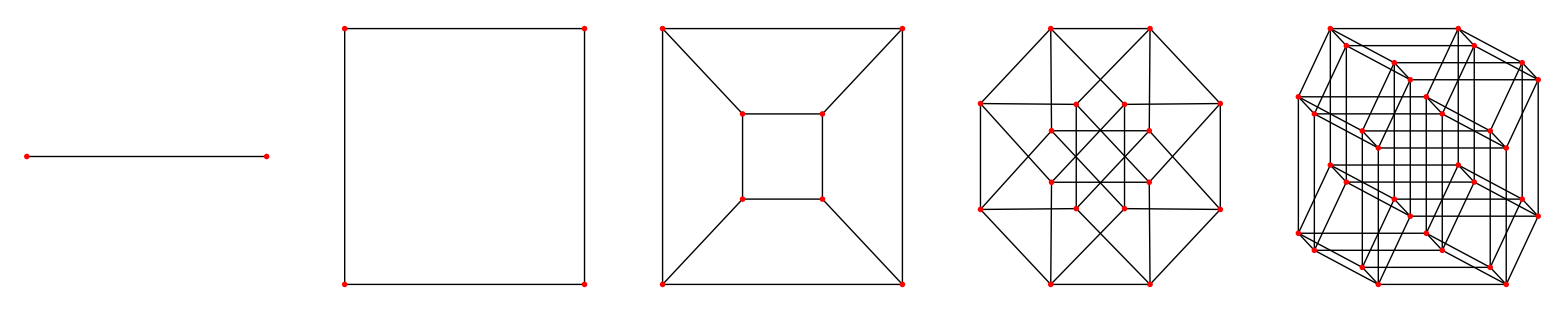

```mathematica
GraphicsRow[Table[GraphData[{"Hypercube",n},"Image"],{n,5}]/.AbsolutePointSize[_]:>AbsolutePointSize[4]]
```

## Special Views

```mathematica
xyCube[4]
```

{{1.,-2.41421,1.,-0.414214},{2.41421,-1.,-0.414214,1.},{1.,-0.414214,1.,-2.41421},{-0.414214,-1.,2.41421,1.},{-1.,-2.41421,-1.,-0.414214},{2.41421,1.,-0.414214,-1.},{1.,0.414214,1.,2.41421},{0.414214,-1.,-2.41421,1.},{-0.414214,1.,2.41421,-1.},{-1.,-0.414214,-1.,-2.41421},{-2.41421,-1.,0.414214,1.},{1.,2.41421,1.,0.414214},{0.414214,1.,-2.41421,-1.},{-1.,0.414214,-1.,2.41421},{-2.41421,1.,0.414214,-1.},{-1.,2.41421,-1.,0.414214}}

```mathematica
v334=nCross[4]
```

{{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1},{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
Show[Isometric[v433=nCube[4]]]
```

⁃Graphics⁃

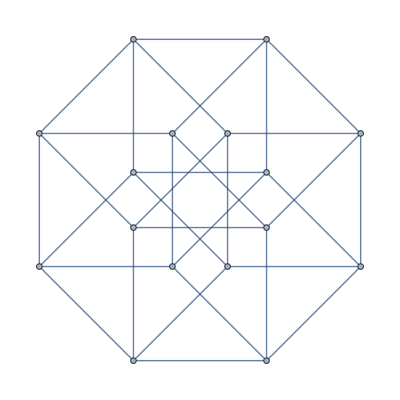

```mathematica
HypercubeGraphIsometric[4]
```

```mathematica
Show[Isometric[xyCube[4]]]
```

⁃Graphics⁃

## Counts of Vertices, Faces, etc.

Nodes

```mathematica
Table[2^n,{n,10}]
```

{2,4,8,16,32,64,128,256,512,1024}

Edges

```mathematica
Table[2^(n-1)n,{n,10}]
```

{1,4,12,32,80,192,448,1024,2304,5120}

Squares

```mathematica
Table[2^(n-3)n(n-1),{n,10}]
```

{0,1,6,24,80,240,672,1792,4608,11520}

Cubes

```mathematica
Table[2^(n-4)n(n-1)(n-2)/3,{n,10}]
```

{0,0,1,8,40,160,560,1792,5376,15360}

## Points Maximizing Product of Distances to Vertices

```mathematica
MaximumProduct[n_]:=Module[{v=Flatten[Outer[List,Sequence@@Table[{0,1},{n}]],n-1],
vars=Array[x,n]},
Maximize[{Times@@(#.#&[vars-#]&/@v),And@@(0≤#≤1&/@vars)},
vars]
]

NMaximumProduct[n_,opts___?OptionQ]:=Module[{v=Flatten[Outer[List,Sequence@@Table[{0,1},{n}]],n-1],
vars=Array[x,n]},
NMaximize[{Times@@(#.#&[vars-#]&/@v),And@@(0≤#≤1&/@vars)},
vars,
opts]
]
```

```mathematica
HypercubeProduct2[l_]:=Module[{n=Length[l],v},v=Flatten[Outer[List,Sequence@@Table[{0,1},{n}]],n-1];
Times@@(#.#&/@(l-#&/@v))
]
```

```mathematica
MaximumProduct[2]//Timing
```

{1.82 Second,{25/256,{x[1]→0,x[2]→1/2}}}

```mathematica
HypercubeProduct2[{0,1/2}]
```

25/256

```mathematica
NMaximumProduct[3]//Timing
```

{1.67 Second,{0.772475,{x[1]→1.,x[2]→1.58019×10^-7,x[3]→0.500143}}}

```mathematica
{#,N[#]}&@HypercubeProduct2[{0,0,1/2}]
```

{50625/65536,0.772476}

```mathematica
MaximumProduct[3]//Timing
```

Uses > 1.7 GB after 2 hours

Runs out of memory...

```mathematica
NMaximumProduct[4]//Timing
```

{12.52 Second,{326.737,{x[1]→1.,x[2]→1.,x[3]→0.499546,x[4]→0.999999}}}

```mathematica
{#,N[#]}&@HypercubeProduct2[{0,0,0,1/2}]
```

{1403336390625/4294967296,326.74}

```mathematica
NMaximumProduct[5]//Timing
```

{18.78 Second,{1.47612×10^9,{x[1]→0.999934,x[2]→0.241092,x[3]→0.998807,x[4]→1.,x[5]→0.998668}}}

```mathematica
NMaximumProduct[5,WorkingPrecision->20]//Timing
```

{5.36 Second,{1.4992208618645384092×10^9,{x[1]→1.,x[2]→0.99946609417111729923,x[3]→0.99936620873636253263,x[4]→0.000091112556628872867824,x[5]→0.27947773448269926383}}}

```mathematica
{#,N[#]}&@HypercubeProduct2[{0,0,0,0,1/4}]
```

{520121694537167720452513764834088049286462890625/340282366920938463463374607431768211456,1.5285×10^9}

```mathematica
Through[{Numerator,Denominator}[{25/256,50625/65536,1403336390625/4294967296,520121694537167720452513764834088049286462890625/340282366920938463463374607431768211456}]]
```

{{25,50625,1403336390625,520121694537167720452513764834088049286462890625},{256,65536,4294967296,340282366920938463463374607431768211456}}